## Fun with Discrete Markov Processes

### Defined by Hector

```mathematica
ExponentialKernel[λ_,distance_]:=λ*ⅇ^(-λ*distance)
(*Markov - Calculates fraction of time mosquitoes spend at each network node, given a Markov process
migrationProbabilities = transitions probability matrix, calculated using Euclidean distances and a Kernel *)

CalculateMarkovSteadyState[migrationProbabilities_]:=Module[{initialState,markov,markovPDF},
initialState=ConstantArray[0,migrationProbabilities//Length]//ReplacePart[#,1->1]&;
markov=DiscreteMarkovProcess[initialState,migrationProbabilities];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length];
markovPDF
]
```

### Basic stuff

```mathematica
(* 
Call DiscreteMarkovProcess with two arguments:
First argument is the initial state;
  Second argument is the transitions matrix;
*)
markovTransitionMatrix = {{0,1/2,1/2},{1/2,0,1/2},{1/2,1/2,0}};
P = DiscreteMarkovProcess[{1,0,0},markovTransitionMatrix];
```

TemporalData[…]

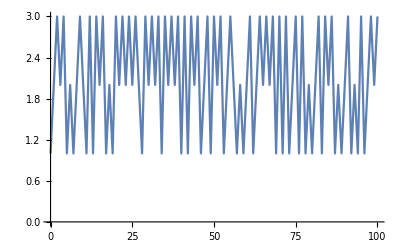

TemporalData[…]

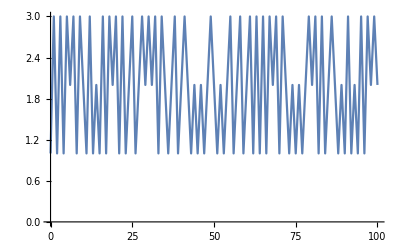

```mathematica
(* Here's how to generate a single trajectory, starting at the defined initial state *)
RandomFunction[P,{0,100}]
ListLinePlot[%]
(* And generate another one *)
RandomFunction[P,{0,100}]
ListLinePlot[%]
```

### Adding mosquito death

```mathematica
(* 
Add a node that represents mosquito death.
Each other node will have a transition probability to death.  For now we will have a constant hazard rate from each one.
To convert our given Transition Matrix we need to add a new element to each row and renormalize accordingly.
*)
markovTransitionMatrix = {{0,1/2,1/2},{1/2,0,1/2},{1/2,1/2,0}};
mosDeathMatrix = Join[Table[Join[markovTransitionMatrix[[i]]*.9,{.1},1],{i,1,Length[markovTransitionMatrix]}],{Join[Table[0,{i,1,Length[markovTransitionMatrix]}],{1.}]},1];

MatrixForm[mosDeathMatrix]
```

(0. | 0.45 | 0.45 | 0.1
0.45 | 0. | 0.45 | 0.1
0.45 | 0.45 | 0. | 0.1
0 | 0 | 0 | 1.)

TemporalData[…]

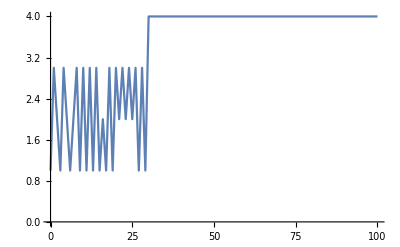

```mathematica
P = DiscreteMarkovProcess[{1,0,0,0},mosDeathMatrix];
SeedRandom[4]
RandomFunction[P,{0,100}]
ListLinePlot[%]
```

### Looking at distributions over time

```mathematica
(* Starting at node 1,
Probability weights after 1 time step *)
init = {1.,0,0,0};
init.mosDeathMatrix
```

{0.,0.45,0.45,0.1}

```mathematica
(* Starting at node 1,
Probability weights after 2 time steps *)
init = {1.,0,0,0};
init.MatrixPower[mosDeathMatrix,2]
```

{0.405,0.2025,0.2025,0.19}

```mathematica
(* Starting at node 1,
Probability weights after 3 time steps *)
init = {1.,0,0,0};
init.MatrixPower[mosDeathMatrix,3]
```

{0.18225,0.273375,0.273375,0.271}

```mathematica
(* Starting at node 1,
Probability weights after 4 time steps *)
init = {1.,0,0,0};
init.MatrixPower[mosDeathMatrix,4]
```

{0.246038,0.205031,0.205031,0.3439}

```mathematica
(* Starting at node 1,
Probability weights after 5 time steps *)
init = {1.,0,0,0};
init.MatrixPower[mosDeathMatrix,5]
```

{0.184528,0.202981,0.202981,0.40951}

```mathematica
h = init.MatrixPower[mosDeathMatrix,5];
h[[1;;-2]]/(1-h[[-1]])
```

{0.3125,0.34375,0.34375}

### Summing time spent at each spot over the lifetime of the mosquito

```mathematica
(* 
The idea here is that "time spent" at a spot is going to be proxy for biting. 
We also have to assume that mosquitoes start out infected, sort of.
*)

(* This will get MUCH trickier once we have different times spent at different locations *)
mosDeathMatrix
```

{{0.,0.45,0.45,0.1},{0.45,0.,0.45,0.1},{0.45,0.45,0.,0.1},{0,0,0,1.}}

```mathematica
init.MatrixPower[mosDeathMatrix,1]
init.MatrixPower[mosDeathMatrix,2]
init.MatrixPower[mosDeathMatrix,3]
init.MatrixPower[mosDeathMatrix,4]
```

{0.,0.45,0.45,0.1}

{0.405,0.2025,0.2025,0.19}

{0.18225,0.273375,0.273375,0.271}

{0.246038,0.205031,0.205031,0.3439}

```mathematica
MatrixForm[Sum[MatrixPower[mosDeathMatrix,i],{i,1,100}]]
init.Sum[MatrixPower[mosDeathMatrix,i],{i,1,100}]
```

(2.79302 | 3.10337 | 3.10337 | 91.0002
3.10337 | 2.79302 | 3.10337 | 91.0002
3.10337 | 3.10337 | 2.79302 | 91.0002
0. | 0. | 0. | 100.)

{2.79302,3.10337,3.10337,91.0002}

```mathematica
(* No idea why this works: *)
mp = mosDeathMatrix;
mp[[-1,-1]]=0;
```

```mathematica
MatrixForm[Inverse[IdentityMatrix[4] - mp].mp]
MatrixForm[init.Inverse[IdentityMatrix[4] - mp].mp]
```

(2.7931 | 3.10345 | 3.10345 | 1.
3.10345 | 2.7931 | 3.10345 | 1.
3.10345 | 3.10345 | 2.7931 | 1.
0. | 0. | 0. | 0.)

(2.7931
3.10345
3.10345
1.)

### Verify by simulating

I want to sum across an ensemble of trajectories, finding the total amount of time spent at each place

```mathematica
MatrixForm[mosDeathMatrix]
MatrixForm[init]
```

(0. | 0.45 | 0.45 | 0.1
0.45 | 0. | 0.45 | 0.1
0.45 | 0.45 | 0. | 0.1
0 | 0 | 0 | 1.)

(1.
0
0
0)

```mathematica
P = DiscreteMarkovProcess[init,mosDeathMatrix];
```

```mathematica
mosEnsemble = RandomFunction[P, {1,100},100000];
```

```mathematica
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,5,1}][[-1]],{i,1,100}];
```

```mathematica
Total[pHistogram,1]/100000.
```

{2.78156,3.08922,3.09281,91.0364}

```mathematica
(* This comes pretty close - it does seem that summing over the number of times the ensemble of trajectories hits each spot corresponds to the quantities calculated above! *)
```

### Adding EIP

```mathematica
(* 
The idea here is that "time spent" at a spot is going to be proxy for biting. 
We also have to assume that mosquitoes start out infected, sort of.

We are going to add an Entomological Incubation Period - we are going to only count the mosquitoes that have a secondary bite after EIP time steps. 
*)
MatrixForm[mosDeathMatrix]
```

(0. | 0.45 | 0.45 | 0.1
0.45 | 0. | 0.45 | 0.1
0.45 | 0.45 | 0. | 0.1
0 | 0 | 0 | 1.)

```mathematica
EIP = 5;
```

```mathematica
(* This is our reduced mosquito death matrix, so that we can sum over it an arbitrary number of times *)
ms = mosDeathMatrix[[;;-2,;;-2]];
MatrixForm[ms]
```

(0. | 0.45 | 0.45
0.45 | 0. | 0.45
0.45 | 0.45 | 0.)

```mathematica
MatrixForm[MatrixPower[ms, EIP]]
```

(0.184528 | 0.202981 | 0.202981
0.202981 | 0.184528 | 0.202981
0.202981 | 0.202981 | 0.184528)

```mathematica
MatrixForm[Sum[MatrixPower[ms, i],{i,1,100}]]
MatrixForm[MatrixPower[ms, EIP].Sum[MatrixPower[ms, i],{i,1,100}]]
MatrixForm[MatrixPower[ms, EIP].Inverse[IdentityMatrix[Length[ms]] - ms].ms]
```

(2.79302 | 3.10337 | 3.10337
3.10337 | 2.79302 | 3.10337
3.10337 | 3.10337 | 2.79302)

(1.77524 | 1.76951 | 1.76951
1.76951 | 1.77524 | 1.76951
1.76951 | 1.76951 | 1.77524)

(1.77529 | 1.76956 | 1.76956
1.76956 | 1.77529 | 1.76956
1.76956 | 1.76956 | 1.77529)

```mathematica
(* Now, simulate this, and see if we get the same thing! *)
init = {1/3.,1/3.,1/3.,0};
P = DiscreteMarkovProcess[init,mosDeathMatrix];
mosEnsemble = RandomFunction[P, {1,100},10000];
```

```mathematica
h = Table[mosEnsemble["SliceData",i],{i,1,100}];
Dimensions[h]
```

{100,10000}

```mathematica
HistogramList[h[[1]],{1,5,1}]
```

{{1,2,3,4,5},{3153,2976,2905,966}}

```mathematica
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,5,1}][[-1]],{i,1,100}];
```

```mathematica
Total[pHistogram,1]/mosEnsemble["PathCount"]*1.
{2.7815600000000003,3.08922,3.09281,91.03641}
```

{3.0109,3.0177,3.0103,90.9611}

{2.78156,3.08922,3.09281,91.0364}

```mathematica
Total[pHistogram[[EIP+1;;]],1]/mosEnsemble["PathCount"]*1.
```

{1.7613,1.7753,1.7816,89.6818}

### Adding EIP, generalized to non-symmetric movement matrix case

```mathematica
mosDeathMatrix = {
{0.,0.1,0.8,0.1},
{0.9/3,0.,0.9*2/3,0.1},
{0.9/3,0.9*2/3,0.,0.1},
{0,0,0,1.}}
```

{{0.,0.1,0.8,0.1},{0.3,0.,0.6,0.1},{0.3,0.6,0.,0.1},{0,0,0,1.}}

```mathematica
EIP = 10;
```

```mathematica
(* This is our reduced mosquito death matrix, so that we can sum over it an arbitrary number of times *)
ms = mosDeathMatrix[[;;-2,;;-2]];
MatrixForm[ms]
```

(0. | 0.1 | 0.8
0.3 | 0. | 0.6
0.3 | 0.6 | 0.)

```mathematica
MatrixForm[MatrixPower[ms, EIP]]
```

(0.087174 | 0.116051 | 0.145453
0.0871681 | 0.11203 | 0.149481
0.0871681 | 0.105983 | 0.155527)

```mathematica
MatrixForm[Sum[MatrixPower[ms, i],{i,1,100}]]
MatrixForm[MatrixPower[ms, EIP].Sum[MatrixPower[ms, i],{i,1,100}]]
MatrixForm[MatrixPower[ms, EIP].Inverse[IdentityMatrix[Length[ms]] - ms].ms]
```

(2.07686 | 2.78839 | 4.13451
2.30763 | 2.65377 | 4.03836
2.30763 | 3.02877 | 3.66336)

(0.784505 | 0.991593 | 1.36193
0.784506 | 0.993102 | 1.36041
0.784506 | 0.995369 | 1.35815)

(0.784525 | 0.991619 | 1.36196
0.784527 | 0.993128 | 1.36045
0.784527 | 0.995396 | 1.35818)

```mathematica
(* Now, simulate this, and see if we get the same thing! *)

(* First initial condition *)
init = {1.,0,0,0};
P = DiscreteMarkovProcess[init,mosDeathMatrix];
mosEnsemble = RandomFunction[P, {1,100},50000];
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,5,1}][[-1]],{i,1,100}];
Total[pHistogram,1]/mosEnsemble["PathCount"]*1.
Total[pHistogram[[EIP+1;;]],1]/mosEnsemble["PathCount"]*1.
```

{2.07058,2.78276,4.11754,91.0291}

{0.78444,0.99176,1.35764,86.8662}

```mathematica
(* Second initial condition *)
init = {0,1.,0,0};
P = DiscreteMarkovProcess[init,mosDeathMatrix];
mosEnsemble = RandomFunction[P, {1,100},50000];
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,5,1}][[-1]],{i,1,100}];
Total[pHistogram,1]/mosEnsemble["PathCount"]*1.
Total[pHistogram[[EIP+1;;]],1]/mosEnsemble["PathCount"]*1.
```

{2.3049,2.66344,4.05484,90.9768}

{0.78876,0.99916,1.37116,86.8409}

```mathematica
(* Third initial condition *)
init = {0,1.,0,0};
P = DiscreteMarkovProcess[init,mosDeathMatrix];
mosEnsemble = RandomFunction[P, {1,100},50000];
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,5,1}][[-1]],{i,1,100}];
Total[pHistogram,1]/mosEnsemble["PathCount"]*1.
Total[pHistogram[[EIP+1;;]],1]/mosEnsemble["PathCount"]*1.
```

{2.29944,2.64188,4.02154,91.0371}

{0.77638,0.98414,1.34936,86.8901}

### Adding EIP, generalized to non-symmetric movement matrix case (larger example)

```mathematica
(* This was generated using Hector's distance-based kernel and penalizations mask *)
mosDeathMatrix ={{0.,0.2459070269699058,0.09756950788048319,0.2459070269699058,0.16768031366488914,0.,0.09756950788048319,0.,0.0453666166343329,0.1},{0.43297145468315135,0.,0.,0.,0.,0.29523674139697964,0.,0.17179180391986906,0.,0.1},{0.208127308987588,0.,0.,0.,0.,0.5245487949685789,0.,0.16732389604383308,0.,0.1},{0.43297145468315135,0.,0.,0.,0.,0.17179180391986906,0.,0.29523674139697964,0.,0.1},{0.22883028227597646,0.,0.,0.,0.,0.3355848588620118,0.,0.3355848588620118,0.,0.1},{0.,0.1395511596199263,0.20465497721408699,0.08120176823785386,0.20465497721408699,0.,0.06528214049995894,0.,0.20465497721408699,0.1},{0.208127308987588,0.,0.,0.,0.,0.16732389604383308,0.,0.5245487949685789,0.,0.1},{0.,0.08120176823785386,0.06528214049995894,0.1395511596199263,0.20465497721408699,0.,0.20465497721408699,0.,0.20465497721408699,0.1},{0.07600786328975707,0.,0.,0.,0.,0.4119960683551214,0.,0.4119960683551214,0.,0.1},{0,0,0,0,0,0,0,0,0,1.}};
```

```mathematica
EIP = 10;
```

```mathematica
(* This is our reduced mosquito death matrix, so that we can sum over it an arbitrary number of times *)
ms = mosDeathMatrix[[;;-2,;;-2]];
MatrixForm[ms]
```

(0. | 0.245907 | 0.0975695 | 0.245907 | 0.16768 | 0. | 0.0975695 | 0. | 0.0453666
0.432971 | 0. | 0. | 0. | 0. | 0.295237 | 0. | 0.171792 | 0.
0.208127 | 0. | 0. | 0. | 0. | 0.524549 | 0. | 0.167324 | 0.
0.432971 | 0. | 0. | 0. | 0. | 0.171792 | 0. | 0.295237 | 0.
0.22883 | 0. | 0. | 0. | 0. | 0.335585 | 0. | 0.335585 | 0.
0. | 0.139551 | 0.204655 | 0.0812018 | 0.204655 | 0. | 0.0652821 | 0. | 0.204655
0.208127 | 0. | 0. | 0. | 0. | 0.167324 | 0. | 0.524549 | 0.
0. | 0.0812018 | 0.0652821 | 0.139551 | 0.204655 | 0. | 0.204655 | 0. | 0.204655
0.0760079 | 0. | 0. | 0. | 0. | 0.411996 | 0. | 0.411996 | 0.)

```mathematica
MatrixForm[MatrixPower[ms, EIP]]
```

(0.10246 | 0. | 0. | 0. | 0. | 0.123109 | 0. | 0.123109 | 0.
0. | 0.0581922 | 0.0480318 | 0.0581922 | 0.075078 | 0. | 0.0480316 | 0. | 0.0611526
0. | 0.058191 | 0.0480324 | 0.0581908 | 0.0750783 | 0. | 0.0480318 | 0. | 0.0611542
0. | 0.0581922 | 0.0480316 | 0.0581922 | 0.075078 | 0. | 0.0480318 | 0. | 0.0611526
0. | 0.058191 | 0.0480321 | 0.058191 | 0.0750783 | 0. | 0.0480321 | 0. | 0.061154
0.102457 | 0. | 0. | 0. | 0. | 0.123111 | 0. | 0.12311 | 0.
0. | 0.0581908 | 0.0480318 | 0.058191 | 0.0750783 | 0. | 0.0480324 | 0. | 0.0611542
0.102457 | 0. | 0. | 0. | 0. | 0.12311 | 0. | 0.123111 | 0.
0. | 0.0581901 | 0.0480323 | 0.0581901 | 0.0750786 | 0. | 0.0480323 | 0. | 0.0611551)

```mathematica
MatrixForm[Sum[MatrixPower[ms, i],{i,1,100}]];
MatrixForm[MatrixPower[ms, EIP].Sum[MatrixPower[ms, i],{i,1,100}]]
MatrixForm[MatrixPower[ms, EIP].Inverse[IdentityMatrix[Length[ms]] - ms].ms]
```

(0.436783 | 0.275636 | 0.227514 | 0.275636 | 0.355624 | 0.524824 | 0.227514 | 0.524824 | 0.289668
0.485315 | 0.248072 | 0.204763 | 0.248072 | 0.320062 | 0.583138 | 0.204763 | 0.583138 | 0.260701
0.485314 | 0.248072 | 0.204763 | 0.248072 | 0.320062 | 0.583139 | 0.204763 | 0.583138 | 0.260701
0.485315 | 0.248072 | 0.204763 | 0.248072 | 0.320062 | 0.583138 | 0.204763 | 0.583138 | 0.260701
0.485314 | 0.248072 | 0.204763 | 0.248072 | 0.320062 | 0.583138 | 0.204763 | 0.583138 | 0.260701
0.436783 | 0.275635 | 0.227514 | 0.275635 | 0.355624 | 0.524825 | 0.227514 | 0.524825 | 0.289668
0.485314 | 0.248072 | 0.204763 | 0.248072 | 0.320062 | 0.583138 | 0.204763 | 0.583139 | 0.260701
0.436783 | 0.275635 | 0.227514 | 0.275635 | 0.355624 | 0.524825 | 0.227514 | 0.524825 | 0.289668
0.485313 | 0.248072 | 0.204763 | 0.248072 | 0.320062 | 0.583139 | 0.204763 | 0.583139 | 0.260702)

(0.436795 | 0.275643 | 0.22752 | 0.275643 | 0.355634 | 0.524838 | 0.22752 | 0.524838 | 0.289675
0.485328 | 0.248078 | 0.204768 | 0.248078 | 0.32007 | 0.583154 | 0.204768 | 0.583153 | 0.260708
0.485327 | 0.248078 | 0.204768 | 0.248078 | 0.32007 | 0.583154 | 0.204768 | 0.583154 | 0.260708
0.485328 | 0.248078 | 0.204768 | 0.248078 | 0.32007 | 0.583153 | 0.204768 | 0.583154 | 0.260708
0.485327 | 0.248078 | 0.204768 | 0.248078 | 0.32007 | 0.583154 | 0.204768 | 0.583154 | 0.260708
0.436794 | 0.275642 | 0.22752 | 0.275642 | 0.355634 | 0.524839 | 0.22752 | 0.524838 | 0.289676
0.485327 | 0.248078 | 0.204768 | 0.248078 | 0.32007 | 0.583154 | 0.204768 | 0.583154 | 0.260708
0.436794 | 0.275642 | 0.22752 | 0.275642 | 0.355634 | 0.524838 | 0.22752 | 0.524839 | 0.289676
0.485326 | 0.248078 | 0.204768 | 0.248078 | 0.32007 | 0.583154 | 0.204768 | 0.583154 | 0.260708)

```mathematica
(* Now, simulate this, and see if we get the same thing! *)
```

```mathematica
(* Averaging over initial conditions *)
init =Table[1./9,10];
init[[-1]]=0;
P = DiscreteMarkovProcess[init,mosDeathMatrix];
mosEnsemble = RandomFunction[P, {1,100},10000];
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,11,1}][[-1]],{i,1,100}];
Total[pHistogram,1]/mosEnsemble["PathCount"]*1.
Total[pHistogram[[EIP+1;;]],1]/mosEnsemble["PathCount"]*1.
(*Cf*)
Total[MatrixPower[ms, EIP].Inverse[IdentityMatrix[Length[ms]] - ms].ms,1]/9
```

{1.3806,0.7502,0.6143,0.7493,0.9523,1.6327,0.627,1.6181,0.7776,90.8979}

{0.4827,0.2642,0.2206,0.263,0.3283,0.5829,0.2246,0.5655,0.275,86.7932}

{0.469149,0.257266,0.212352,0.257266,0.331925,0.563715,0.212352,0.563715,0.270364}

```mathematica
(* First initial condition *)
init =Table[0,10];
init[[1]]=1;
P = DiscreteMarkovProcess[init,mosDeathMatrix];
RandomSeed[2];
mosEnsemble = RandomFunction[P, {1,100},10000];
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,11,1}][[-1]],{i,1,100}];
Total[pHistogram,1]/mosEnsemble["PathCount"]*1.
Total[pHistogram[[EIP+1;;]],1]/mosEnsemble["PathCount"]*1.
(*Cf*)
(MatrixPower[ms, EIP].Inverse[IdentityMatrix[Length[ms]] - ms].ms)[[1]]
```

{1.3245,0.9019,0.6243,0.8946,1.0047,1.477,0.6257,1.4974,0.7143,90.9356}

{0.4418,0.2916,0.2243,0.2776,0.3635,0.5422,0.2301,0.5295,0.2887,86.8107}

{0.436795,0.275643,0.22752,0.275643,0.355634,0.524838,0.22752,0.524838,0.289675}

```mathematica
(* Second initial condition *)
init =Table[0,10];
init[[2]]=1;
P = DiscreteMarkovProcess[init,mosDeathMatrix];
RandomSeed[0];
mosEnsemble = RandomFunction[P, {1,100},50000];
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,11,1}][[-1]],{i,1,100}];
Total[pHistogram,1]/mosEnsemble["PathCount"]*1.
Total[pHistogram[[EIP+1;;]],1]/mosEnsemble["PathCount"]*1.
(*Cf*)
(MatrixPower[ms, EIP].Inverse[IdentityMatrix[Length[ms]] - ms].ms)[[2]]
```

{1.58312,0.74608,0.5893,0.73402,0.90826,1.64472,0.5732,1.51186,0.71516,90.9943}

{0.48688,0.25188,0.20724,0.24734,0.31262,0.58392,0.20676,0.582,0.26086,86.8605}

{0.485328,0.248078,0.204768,0.248078,0.32007,0.583154,0.204768,0.583153,0.260708}

```mathematica
(* Third initial condition *)
init =Table[0,10];
init[[3]]=1;
P = DiscreteMarkovProcess[init,mosDeathMatrix];
RandomSeed[0];
mosEnsemble = RandomFunction[P, {1,100},50000];
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,11,1}][[-1]],{i,1,100}];
Total[pHistogram,1]/mosEnsemble["PathCount"]*1.
Total[pHistogram[[EIP+1;;]],1]/mosEnsemble["PathCount"]*1.
(*Cf*)
(MatrixPower[ms, EIP].Inverse[IdentityMatrix[Length[ms]] - ms].ms)[[3]]
```

{1.32894,0.7147,0.62162,0.69628,0.91868,1.90062,0.5668,1.51858,0.75318,90.9806}

{0.48228,0.2438,0.20376,0.25082,0.32022,0.5842,0.20696,0.58584,0.25934,86.8628}

{0.485327,0.248078,0.204768,0.248078,0.32007,0.583154,0.204768,0.583154,0.260708}

### Adding interventions:

Suppose I now want to add in some interventions, that kill mosquitoes faster when they hit certain spots.
In our example, I can make it so that if a mosquito reaches spot 2 then it has a 90% chance of dying instead of a 10% chance of dying.
Need to generalize out the way that we convert the transitions matrix into the mosquito death matrix.

```mathematica
markovTransitionMatrix = {{0,1/2,1/2},{1/2,0,1/2},{1/2,1/2,0}};
mosHazardRates = {0.1, 0.9,0.1};
mosDeathMatrix = Join[Table[Join[markovTransitionMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[markovTransitionMatrix]}],{Join[Table[0,{i,1,Length[markovTransitionMatrix]}],{1.}]},1];
```

```mathematica
(* Unsure of these results - how about simulating? *)
```

```mathematica
P = DiscreteMarkovProcess[init,mosDeathMatrix];
```

```mathematica
mosEnsemble = RandomFunction[P, {1,100},100000];
```

```mathematica
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,5,1}][[-1]],{i,1,100}];
```

```mathematica
Total[pHistogram,1]/100000.
```

{0.33736,0.89354,0.6492,98.1199}

```mathematica
mosEnsemble = RandomFunction[P, {0,10},1000];
```

```mathematica
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,5,1}][[-1]],{i,1,10}];
```

```mathematica
Total[pHistogram,1]/1000.
```

{0.348,0.884,0.669,8.099}

Trying again with a larger matrix, to see just how asymmetric things get

```mathematica
markovTransitionMatrix  = 1/9.*(1 - IdentityMatrix[10]);
mosHazardRates = Table[0.1,{i,1,10}];
mosHazardRates[[4]] = 0.9;
mosHazardRates[[7]] = 0.9;
init = Table[0,{i,1,11}];
init[[1]] = 1;
```

```mathematica
mosDeathMatrix = Join[Table[Join[markovTransitionMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[markovTransitionMatrix]}],{Join[Table[0,{i,1,Length[markovTransitionMatrix]}],{1.}]},1];
MatrixForm[mosDeathMatrix]
```

(0. | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.1 | 0. | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.1 | 0.1 | 0. | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.0111111 | 0.0111111 | 0.0111111 | 0. | 0.0111111 | 0.0111111 | 0.0111111 | 0.0111111 | 0.0111111 | 0.0111111 | 0.9
0.1 | 0.1 | 0.1 | 0.1 | 0. | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0. | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.0111111 | 0.0111111 | 0.0111111 | 0.0111111 | 0.0111111 | 0.0111111 | 0. | 0.0111111 | 0.0111111 | 0.0111111 | 0.9
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0. | 0.1 | 0.1 | 0.1
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0. | 0.1 | 0.1
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0. | 0.1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
Length[{.1,.1,.1,.1,.1,.1,.1,.1,.1,0}]
{.1,.1,.1,.1,.1,.1,.1,.1,.1,.1,0}.Inverse[IdentityMatrix[11] - mp].mp
```

10

{0.26255,0.26255,0.26255,0.294422,0.26255,0.26255,0.294422,0.26255,0.26255,0.26255,1.}

```mathematica
(* And the time spent over each mosquito's lifetime *)
(* No idea why this works: *)
mp = mosDeathMatrix;
mp[[-1,-1]]=0;
MatrixForm[Inverse[IdentityMatrix[11] - mp].mp]
MatrixForm[init.Inverse[IdentityMatrix[11] - mp].mp]
MatrixForm[{.1,.1,.1,.1,.1,.1,.1,.1,.1,.1,0}.Inverse[IdentityMatrix[11] - mp].mp]
```

(0.238682 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.329591 | 1.
0.329591 | 0.238682 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.329591 | 1.
0.329591 | 0.329591 | 0.238682 | 0.358566 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.329591 | 1.
0.0398406 | 0.0398406 | 0.0398406 | 0.0323541 | 0.0398406 | 0.0398406 | 0.0433431 | 0.0398406 | 0.0398406 | 0.0398406 | 1.
0.329591 | 0.329591 | 0.329591 | 0.358566 | 0.238682 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.329591 | 1.
0.329591 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.238682 | 0.358566 | 0.329591 | 0.329591 | 0.329591 | 1.
0.0398406 | 0.0398406 | 0.0398406 | 0.0433431 | 0.0398406 | 0.0398406 | 0.0323541 | 0.0398406 | 0.0398406 | 0.0398406 | 1.
0.329591 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.358566 | 0.238682 | 0.329591 | 0.329591 | 1.
0.329591 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.238682 | 0.329591 | 1.
0.329591 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.238682 | 1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

(0.238682
0.329591
0.329591
0.358566
0.329591
0.329591
0.358566
0.329591
0.329591
0.329591
1.)

(0.26255
0.26255
0.26255
0.294422
0.26255
0.26255
0.294422
0.26255
0.26255
0.26255
1.)

```mathematica
(* Verifying the weirdness with simulations *)
P = DiscreteMarkovProcess[init,mosDeathMatrix];
mosEnsemble = RandomFunction[P, {0,10},10000];
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,12,1}][[-1]],{i,1,10}];
```

```mathematica
Total[pHistogram,1]/1000.
```

{2.237,3.217,3.187,3.519,3.196,3.136,3.429,3.068,3.159,3.21,68.642}